Solution to the irrotational keyhole problem:

```mathematica
ϕ[r_,θ_]:= U * (r+a^2/r)Cos[θ];
```

Parameters for the keyhole problem:

```mathematica
U=0.1;
a = 0.05;
```

```mathematica
Clear[r,θ];
ϕr[r_,θ_]=D[ϕ[r,θ],r]; ϕθ[r_,θ_]=D[ϕ[r,θ],θ];
```

```mathematica
xf=TransformedField["Polar"->"Cartesian",ϕ[r,θ],{r,θ}->{x,y}];
```

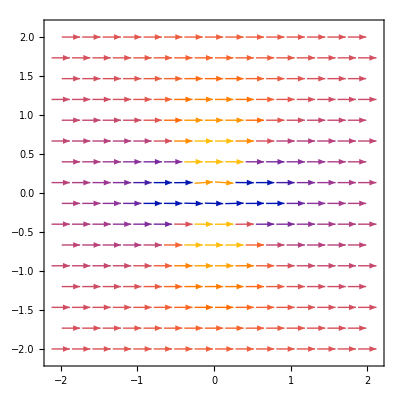

```mathematica
VectorPlot[{ϕr[Sqrt[x^2+y^2],ArcTan[y/x]]*Cos[ArcTan[y/x]]-1/Sqrt[x^2+y^2] ϕθ[Sqrt[x^2+y^2],ArcTan[y/x]]Sin[ArcTan[y/x]],ϕr[Sqrt[x^2+y^2],ArcTan[y/x]]*Sin[ArcTan[y/x]]+1/Sqrt[x^2+y^2] ϕθ[Sqrt[x^2+y^2],ArcTan[y/x]]Cos[ArcTan[y/x]]},{x,-2,2},{y,-2, 2}]
```

```mathematica
{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}
```

{{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}}

```mathematica
Inverse[%]
```

{{Cos[θ]/(Cos[θ]^2+Sin[θ]^2),-Sin[θ]/(Cos[θ]^2+Sin[θ]^2)},{Sin[θ]/(Cos[θ]^2+Sin[θ]^2),Cos[θ]/(Cos[θ]^2+Sin[θ]^2)}}

```mathematica
FullSimplify[%]
```

{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}

```mathematica
ϕxy[x_,y_]:=x+x/(x^2+y^2); ϕx[x_,y_]= D[ϕxy[x,y],x];
ϕy[x_,y_] = D[ϕxy[x,y],y];
```

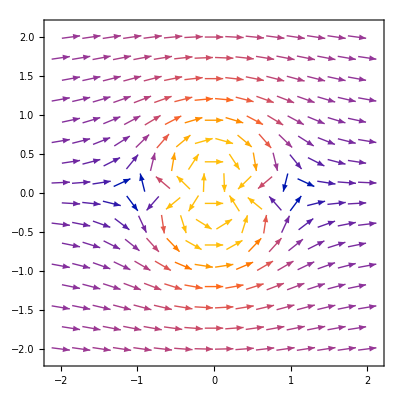

```mathematica
VectorPlot[{ϕx[x,y],ϕy[x,y]},{x,-2,2},{y,-2,2}]
```

Streamlines around the simple keyhole model:

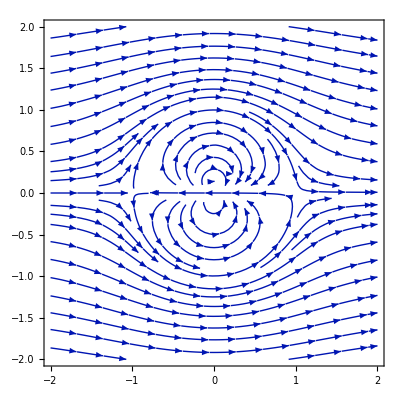

```mathematica
StreamPlot[{ϕx[x,y],ϕy[x,y]},{x,-2,2},{y,-2,2}]
```